```mathematica
Needs["HierarchicalClustering`"]
SetOptions[Plot,ImageSize->Large,PlotStyle->{Black,Thick},BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->24}];
SetOptions[MatrixPlot,ImageSize->Small,BaseStyle->{FontFamily->"SansSerif",Bold}];
SetOptions[ParametricPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->19}];
SetOptions[ListPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold},PlotStyle->{Thick,Black},PlotMarkers->None,Filling->Axis];
```

Film dynamics of a non evaporating liquid film with Rayleigh-Taylor instability (results in Pendant drop and satellite drop formation)

```mathematica
DynamicModule[{x,t,xMin=0, xMax=2.Pi(Sqrt[2]/1),TMax = 80,frac=0.99,m,time},   hsol=u /. NDSolve[{D[u[t, x], t] == -D[u[t, x]^3*D[u[t, x], x, x, x], x] - 
        D[u[t, x]^3*D[u[t, x], x], x], u[0, x] == 1 - 0.1*Sin[1*(x/Sqrt[2])], 
      Derivative[0, 1][u][t, xMin] == Derivative[0, 1][u][t, xMax], 
      Derivative[0, 2][u][t, xMin] == Derivative[0, 2][u][t, xMax], 
      Derivative[0, 3][u][t, xMin] == Derivative[0, 3][u][t, xMax], 
      u[t, xMin] == u[t, xMax]}, u, {t, 0, TMax}, {x, xMin, xMax}, 
     MaxStepSize -> 0.1, Method -> "LSODA"][[1]];

Plot[hsol[TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"}];
Manipulate[Plot[hsol[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}}],{time,0,1,0.01}]
]
```

Base case: liquid film on a non-porous substrate with thermocapillarity (desatbilizing), surface tension (stabilizing) and gravity(stabilizing).  Thermocapillary fingers form.

```mathematica
DynamicModule[{x,t,xMin=-Pi/0.0677, xMax= Pi/0.0677,k = 0.0677, 
TMax = 2000.,fractionOfTMax},
 hbase= u /. NDSolve[{D[u[t, x], t] == -100*D[u[t, x]^3*D[u[t, x], x, x, x], x] + 
        (1/3)*D[u[t, x]^3*D[u[t, x], x], x] - 
        5*D[(u[t, x]/(1 + u[t, x]))^2*D[u[t, x], x], x], 
      u[0, x] == 1 - 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
      Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], 
      Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
      Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, 
     {x, xMin, xMax}, MaxSteps -> 100000, Method -> {"MethodOfLines", 
       "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
        {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, 
         "DifferenceOrder" -> 5}}][[1]];

Manipulate[Plot[hbase[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}},GridLines->Automatic],{time,0,1,0.05}]
]
```

Base case with zero gravity.  Thermocapillary fingers grow to larger amplitudes in zero gravity, for the same values of S and M.  A balance is struck between surface tension stabilization and thermocapillary destabilization.  Large values of S lead to deccelerated growth of long wave instabilities.

```mathematica
DynamicModule[{x,t,xMin=-Pi/0.0677, xMax= Pi/0.0677,k = 0.0677, 
TMax = 2000.,fractionOfTMax},
 hbase0= u /. NDSolve[{D[u[t, x], t] == -100*D[u[t, x]^3*D[u[t, x], x, x, x], x] + 
        (0/3)*D[u[t, x]^3*D[u[t, x], x], x] - 
        5*D[(u[t, x]/(1 + u[t, x]))^2*D[u[t, x], x], x], 
      u[0, x] == 1 - 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
      Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], 
      Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
      Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, 
     {x, xMin, xMax}, MaxSteps -> 100000, Method -> {"MethodOfLines", 
       "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
        {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, 
         "DifferenceOrder" -> 5}}][[1]];

Manipulate[Plot[hbase0[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}},PlotStyle->{Thick,Red},GridLines->Automatic],{time,0,1,0.05}]
]
```

Base case with with a porous substrate.  Porous substrate imbibes the film completely.

```mathematica
DynamicModule[{x,t,xMin=-Pi/0.0677, xMax= Pi/0.0677,k = 0.0677, 
TMax = 2000.,mult=1.,Pm=0.025,Ga=1./3.,fractionOfTMax},
 hbasep= u /. NDSolve[{D[u[t, x], t] == -100*D[u[t, x]^3*D[u[t, x], x, x, x], x] + 
        (1./3.)*D[u[t, x]^3*D[u[t, x], x], x] - 
        5*D[(u[t, x]/(1 + u[t, x]))^2*D[u[t, x], x], x]+ mult*Pm*(D[u[t, x], x, x] - Ga*u[t, x]), 
      u[0, x] == 1 - 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
      Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], 
      Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
      Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, 
     {x, xMin, xMax}, MaxSteps -> 100000, Method -> {"MethodOfLines", 
       "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
        {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, 
         "DifferenceOrder" -> 5}}][[1]];

Manipulate[Plot[hbasep[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}},PlotStyle->{Thick,Black},GridLines->Automatic],{time,0,1,0.05}]
]
```

Base case with zero gravity and a porous substrate: Damping of secondary structures and long time sustenance of primary structures.

```mathematica
DynamicModule[{x,t,xMin=-Pi/0.0677, xMax= Pi/0.0677,k = 0.0677, 
TMax = 12000.,mult=1.,Pm=0.15,Ga=0./3.,fractionOfTMax},
 hbasep0= u /. NDSolve[{D[u[t, x], t] == -100*D[u[t, x]^3*D[u[t, x], x, x, x], x] + 
        (0./3.)*D[u[t, x]^3*D[u[t, x], x], x] - 
        5*D[(u[t, x]/(1 + u[t, x]))^2*D[u[t, x], x], x]+ mult*Pm*(D[u[t, x], x, x] - Ga*u[t, x]), 
      u[0, x] == 1 - 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
      Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], 
      Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
      Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, 
     {x, xMin, xMax}, MaxSteps -> 100000, Method -> {"MethodOfLines", 
       "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
        {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, 
         "DifferenceOrder" -> 5}}][[1]];

Manipulate[Plot[hbasep0[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}},PlotStyle->{Thick,Black},GridLines->Automatic],{time,0,1,0.05}]
]
```

Comparison of base case and zero gravity case. With zero gravity, film dynamics are accelerated.  Recurrence plots may be used to visualize the spatial structural differences at different times.  Recurrence plots provide intuitive qualitative information.

```mathematica
xMin=-Pi/0.0677; xMax= Pi/0.0677;TMax=2000.;
Manipulate[
Plot[{hbase[fraction TMax,x],hbase0[fraction TMax,x]},{x,xMin,xMax},PlotStyle->{{Thick,Black},{Thick,Red}},PlotLegends->{"Base case","Zero Gravity"},PlotRange->{{xMin,xMax},{0,3.2}}]
,{fraction,0,1,0.05}]
```

Comparison of base case with base+0g and base+0g+porosity (profile plots and recurrence plots)

```mathematica
xMin=-Pi/0.0677; xMax= Pi/0.0677;TMax=2000.;TMaxp=12000.;
Manipulate[
Plot[{hbase[fraction TMax,x],hbase0[fraction TMax,x],hbasep0[fraction TMax,x]},{x,xMin,xMax},PlotStyle->{{Thick,Black},{Thick,Red},{Thick,RGBColor[0.49,0.52,0.36]}},PlotLegends->{"Base case, non porous substrate","Zero Gravity, non porous substrate","Zero Gravity, porous substrate"},PlotRange->{{xMin,xMax},{0,3.2}}]
,{fraction,0,1,0.025}]
```

```mathematica
Manipulate[g11=With[{stepSize=.4,end=xMax,fraction=np},
MatrixPlot[UnitStep[0.0001-DistanceMatrix[hbase[ fraction TMax,Range[xMin,end,stepSize]]]],ColorFunction->"Monochrome",Frame->True,FrameLabel->{"","Base \n(Krishnamoorthy et al. 1995)"}]
];
g12=With[{stepSize=0.15,end=xMax,fraction=np},
MatrixPlot[UnitStep[0.0001-DistanceMatrix[hbase0[fraction TMax,Range[xMin,end,stepSize]]]],ColorFunction->"Monochrome",Frame->True,FrameLabel->{"","Base + 0g \n(Narendranath et al. 2015)"}]];
g13=With[{stepSize=0.15,end=xMax,fraction=np},
MatrixPlot[UnitStep[0.0001-DistanceMatrix[hbasep0[fraction TMax,Range[xMin,end,stepSize]]]],ColorFunction->"Monochrome",Frame->True,FrameLabel->{"","Base + 0g + porosity \n (Narendranath et al. 2016)" }]
];
GraphicsGrid[{{g11,g12,g13}}],{np,0,1,0.05}]
```

Linear stability analysis of full evolution equation.  The growth rate of long wave instabilities as per linear stability analysis is given by:

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm];
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn;
```

For the Pendant drop case, with M=0, Pm=0, Ga=1, Sn=1, we reduce the growth rate equation to a quartic equation of the form f = μ q^2-q^4. The parameter μ=-Ga/Sn, sometimes called the Bond number in liquid film evolution equation literature.  Plotting the growth rate and a stream plot for the growth rate suggests the presence of a stationary point.  This stationary point may be evaluated as the roots of the growth rate equation, i.e., Roots[f=0]

Growth rate (f) equation:

0.+0.333333 q^2-1. q^4

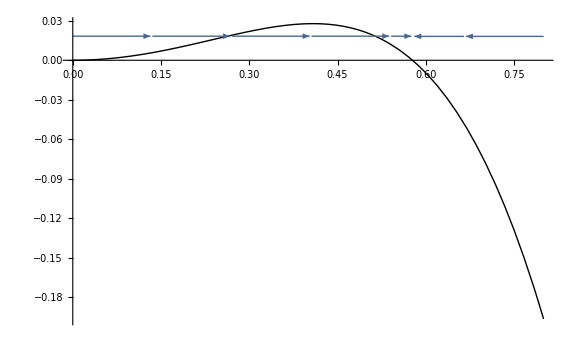

Roots of growth rate equation (stationary points):

{{q→-0.57735},{q→0.},{q→0.},{q→0.57735}}

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm];
Bi=0.;M=0.;Pm=0.;
Ga=-1.;Sn=1.;
Print["Growth rate (f) equation: "]
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn

Show[Plot[f,{q,0,0.8},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{f,0},{q,0,0.8},{y,0,0.1},GridLines->Automatic,StreamScale->Medium]
]

Print["Roots of growth rate equation (stationary points): "]
Quiet[Solve[f==0,q]]
```

The general growth rate equation and its roots may be used to uncover subcritical pitchfork bifurcation.  The stereotypical equation that leads to subcrit. pitchfork bif. is f(x,μ) = μ x-x^3.

Growth rate (f) equation:

0.-(Ga q^2)/3-q^4 Sn

Roots of growth rate equation (stationary points):

{q→0.,q→0.,q→-((0.+0.57735 ⅈ) √Ga)/(√Sn),q→((0.+0.57735 ⅈ) √Ga)/(√Sn)}

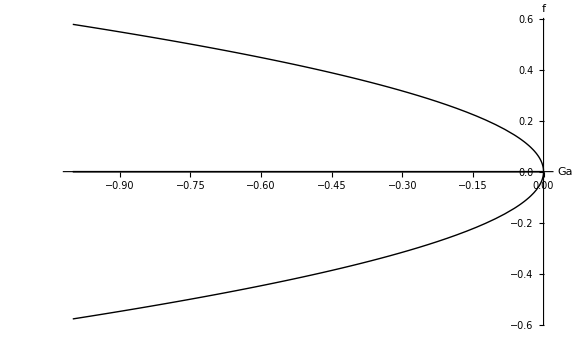

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm,roots];
Bi=0.;M=0.;Pm=0.;
Print["Growth rate (f) equation: "]
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn
Print["Roots of growth rate equation (stationary points): "]
roots=Quiet[Solve[f==0,q]//Flatten]
Sn=1.0;
Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]},{Ga,-1,0},PlotStyle->{{Thick,Black},{Thick,Black}},AxesLabel->{"Ga","f"}]
```

A potential of the form -dV/dx = f(x,μ) is defined to ascertain stability.  For μ=-Ga/Sn<0 the situation is unstable as evidenced by the vectors driving and the slope of the potential.  Non negative values of μ are not probed when considering the case of Pendant drop formation.  It suffices to say that for negative values of μ, f(x,,μ)=μ x-x^3 represents an unstable situation. The potential “well” suggests that any vector along the well slides off - it is not stable.

 A non-negative value of μ would lead to a stable situation.

x^5/5-(x^3 μ)/3

{0,0,-√μ,√μ}

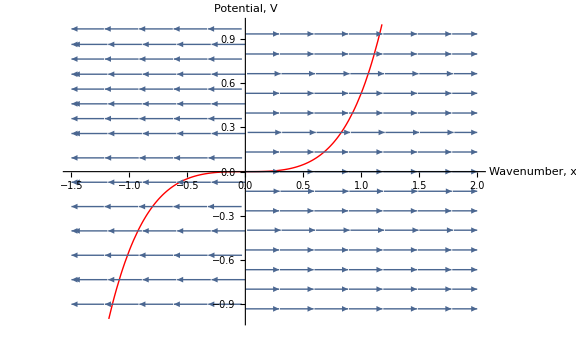

```mathematica
Clear[f,μ,x,λ,roots,μmin,μmax,xmin,xmax,ymin,ymax];
f=μ x^2-x^4 ;
V=-Integrate[f,x]
roots=Quiet[Solve[f==0,x]]//Flatten;
{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]}
μmin=-2;μmax=2;
xmin=-1.5;xmax=2;ymin=-1;ymax=1;
μ=-1.;
Show[
Plot[V,{x,xmin,xmax},PlotStyle->{Thick,Red},PlotRange->{{xmin,xmax},{ymin,ymax}},AxesLabel->{"Wavenumber, x","Potential, V"}],
StreamPlot[{V,0},{x,xmin,xmax},{y,-1,1}]
]
```

Non - negative value of μ (Ga/Sn > 1) is shown here. A stable stationary point exists at Sqrt[μ].  Essentially, both gravity and surface tension are stabilizing.  Any disturbances on the film surface are effectively damped.  Long wave instabilities do not arise.  The potential well suggests that any vector on the surface of this potential slides towards the stable point. “All roads lead to the stable point Sqrt[μ]”

{x→0,x→0,x→-√μ,x→√μ}

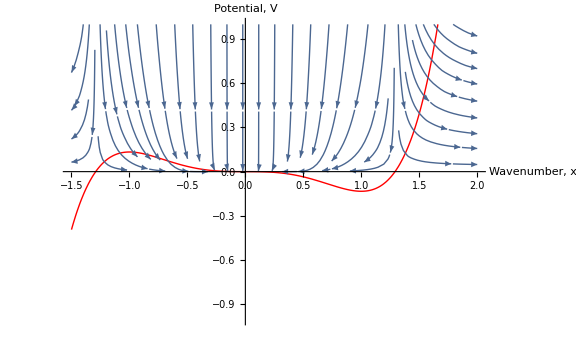

```mathematica
Clear[f,μ,x,λ,roots,μmin,μmax,xmin,xmax,ymin,ymax];
f=μ x^2-x^4 ;
V=-Integrate[f,x];
roots=Quiet[Solve[f==0,x]]//Flatten
{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]};
μmin=-2;μmax=2;
xmin=-1.5;xmax=2;ymin=-1;ymax=1;
μ=1;
Show[
Plot[V,{x,xmin,xmax},PlotStyle->{Thick,Red},PlotRange->{{xmin,xmax},{ymin,ymax}},AxesLabel->{"Wavenumber, x","Potential, V"}],
StreamPlot[{V,-y},{x,xmin,xmax},{y,0,1},GridLines->Automatic,StreamScale->Medium]
]
```

Next, I consider the growth rate equation for the entire gamut of mechanisms, viz., surface tension (stabilizing), gravity (stabilizing), thermocapillarity (stabilizing) and Porosity of substrate (stabilization through imbibition).  The equation for growth rate takes the form: 
f(μ,λ,x)=μ x^2-x^4 + λ. Here, μ=(1/Sn)(M/(1+Bi)^2-Pm-Ga) while λ=(-Pm Ga/Sn).  

When λ=0, we could either have Ga or Pm as being zero (or both).  The fourth order term is surface tension while the 2nd order term.  The effect of gravity is captured through the parameter μ that multiplies the second order term.

Supercritical pitchfork bifurcation is depicted for a representative value of λ=0.0 with μ as the parameter.

0.-x^4+x^2 μ

{x→0.,x→0.,x→-1. √μ,x→√μ}

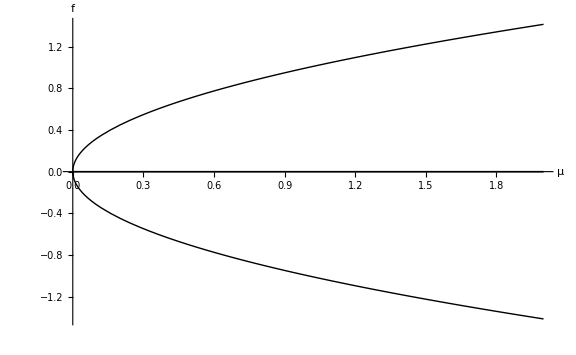

```mathematica
Clear[f,μ,x,λ,roots,μmin,μmax,xmin,xmax,ymin,ymax,Ga,Bi,M,Sn,Pm];
(*μ=(1/Sn)(M/(1+Bi)^2-Pm-Ga);
λ=(-Pm Ga/Sn);*)
λ=0.;
f=μ x^2-x^4 + λ;
Collect[f,x^2]
roots=Quiet[Solve[f==0,x]]//Flatten
Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]},{μ,0,2},PlotStyle->{{Thick,Black},{Thick,Black}},AxesLabel->{"μ","f"}]
```

Again, a potential is defined and plotted along with vectors.  For typical values as per Narendranath et al., Oron et al., Krishnamoorthy et al., for non-porous substrate (with Ga=0 or Ga=1.0), the supercritical pitchfork bifurcation shows instability.  This was already encountered through the formation of thermocapillary finger structures that lead to rupture the film.

0.00289256 x^3+x^5/5

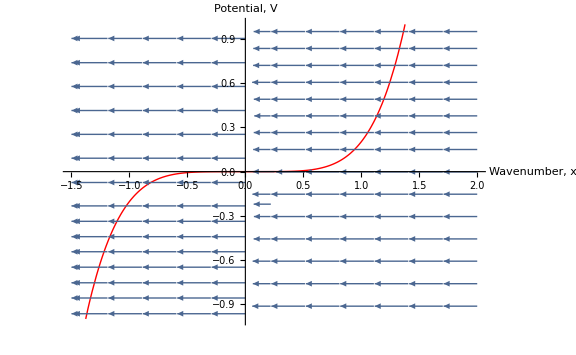

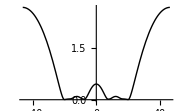

{{x→0.},{x→0.},{x→0.-0.0931541 ⅈ},{x→0.+0.0931541 ⅈ}}

```mathematica
Clear[f,μ,x,λ,roots,μmin,μmax,xmin,xmax,ymin,ymax,Ga,Bi,M,Sn,Pm];
f=μ x^2-x^4+λ ;
μ=(1/Sn)(M/(1+Bi)^2-Pm-Ga);
(*λ=(-Pm Ga/Sn);*)
λ=0.;

μmin=-2;μmax=2;
xmin=-1.5;xmax=2;ymin=-1;ymax=1;
Sn=100.;Ga=5.;M=5.;Pm=0.;Bi=0.1;
V=-Integrate[f,x]
μ;
Show[
Plot[V,{x,xmin,xmax},PlotStyle->{Thick,Red},PlotRange->{{xmin,xmax},{ymin,ymax}},AxesLabel->{"Wavenumber, x","Potential, V"}],
StreamPlot[{f,0},{x,xmin,xmax},{y,-1,1},GridLines->Automatic]
]
{xMin=-Pi/0.0677, xMax= Pi/0.0677,TMax=1650};
Plot[hbase[TMax,x],{x,xMin,xMax},ImageSize->Small]
Solve[f==0,x]
```

However, with Ga = 1. and Pm > 0, we still have instability and the formation of thermocapillary structures.  The vectors continue to “slide off” the potential surface.  However, when the surface tension is reduced from S=100 to S=10

-0.0137741 x^3+x^5/5

0.+0.0413223 x^2-x^4

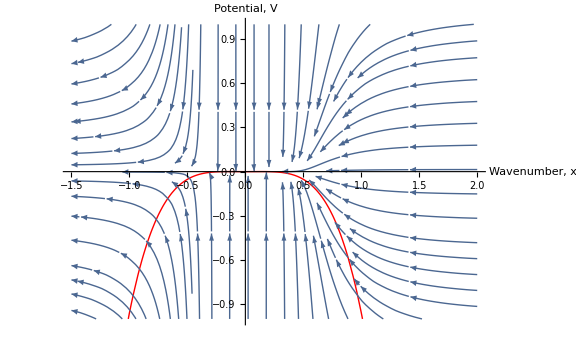

```mathematica
Clear[f,μ,x,λ,roots,μmin,μmax,xmin,xmax,ymin,ymax,Ga,Bi,M,Sn,Pm];
f=μ x^2-x^4+λ ;
μ=(1/Sn)(M/(1+Bi)^2-Pm-Ga);

V=-Integrate[f,x];
μmin=-2;μmax=2;
xmin=-1.5;xmax=2;ymin=-1;ymax=1;
Sn=100.;Ga=0.;M=5;Pm=0.;Bi=0.1;
μ;
λ=(-Pm Ga/Sn);
V=-Integrate[f,x]
f
Show[
Plot[f,{x,xmin,xmax},PlotStyle->{Thick,Red},PlotRange->{{xmin,xmax},{ymin,ymax}},AxesLabel->{"Wavenumber, x","Potential, V"}],
StreamPlot[{f,-y},{x,xmin,xmax},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```

Comparison of recurrence matrices

0. | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4 | 0.45 | 0.5 | 0.55 | 0.6 | 0.65 | 0.7 | 0.75 | 0.8 | 0.85 | 0.9 | 0.95 | 1.
0. | 30.2985 | 38.6264 | 42.2847 | 44.1588 | 43.8862 | 41.2795 | 51.788 | 58.7537 | 48.621 | 48.7852 | 57.4456 | 72.4707 | 59.95 | 58.6003 | 57.6368 | 63.7809 | 65.7571 | 65.7267 | 66.888 | 69.1375

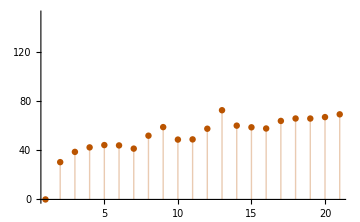

```mathematica
With[{stepSize=0.3,end=xMax},
mbase=Table[UnitStep[0.0001-DistanceMatrix[hbase[fraction TMax,Range[xMin,end,stepSize]]]],{fraction,0,1,0.05}];
mbase0=Table[UnitStep[0.0001-DistanceMatrix[hbase0[fraction TMax,Range[xMin,end,stepSize]]]],{fraction,0,1,0.05}];]
idx=Table[f,{f,0,1,0.05}];
tt=ParallelTable[Norm[mbase[[i]]-mbase0[[i]],"Frobenius"]//N,{i,1,Dimensions[mbase][[1]],1}];
TableForm[{idx,tt}]
p0x30=ListPlot[tt,PlotStyle->{RGBColor[0.73,0.33,0.0]},PlotRange->{All,{0,150}}]
```